Autor: Krzysztof Dragon

# Metody numeryczne w technice

## (kierunek informatyka)

## Projekt 7

Metoda różnic skończonych

Napisać procedurę realizującą metodę różnic skończonych dla zagadnienia brzegowego liniowego równania różniczkowego zwyczajnego rzędu drugiego. Działanie procedury przetestować na przykładzie podanym na wykładzie.

Korzystając z napisanej procedury wyznaczyć rozwiązanie przybliżone zagadnienia brzegowego:

{m y''(x)+ k y'(x) +s y(x)=0,  x∈[0,10],
y(0)=1, y(10)=1,

Obliczenia wykonać dla dwóch zestawów danych:
a) m=1, k=3, s=2;
b) m=5, k=2, s=10.

Za każdym razem obliczenia wykonać dla 500 i 1000 kroków.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązania przybliżone. (*)
Wykreślić także, na jednym rysunku, błędy uzyskanych rozwiązań przybliżonych.
Policzyć ponadto błędy maksymalne oraz średnie dla obu siatek oraz zestawić je na wykresie słupkowym, np. postaci:

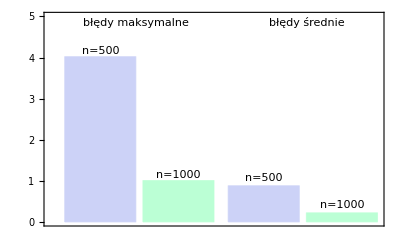

-Graphics-

## Rozwiązanie

```mathematica
Clear[mrsWM]
(* Metoda różnic skończonych dla zagadnienia brzegowego liniowego równania różniczkowego zwyczajnego rzędu drugiego *)
mrsWM[ad_,bd_,cd_,dd_,α1_,α2_,β1_,β2_,t1_,t2_,a_,b_,n_]:=Module[{h,xw,ak,bk,i,j,yw,wyn},
h = (b-a)/n;
xw = Table[a+i*h,{i,0,n}];
ak = Table[0,{i,0,n},{j,0,n}];
bk=Table[0,{i,0,n}];

bk[[1]]=2*h*t1;
bk[[n+1]] = 2*h*t2;
ak[[1,1]]= 2h*α1-3*α2;
ak[[1,2]] = 4*α2;
ak[[1,3]] = -α2;

ak[[n+1,n-1]] = β2;
ak[[n+1,n]] = -4*β2;
ak[[n+1,n+1]] = 2*h*β1+3*β2;

Do[bk[[i]] = 2*h^2*dd[xw[[i]]];
ak[[i,i-1]] = 2*ad[xw[[i]]] - h*bd[xw[[i]]];
ak[[i,i]] = 2*h^2*cd[xw[[i]]] - 4*ad[xw[[i]]];
ak[[i,i+1]] = 2*ad[xw[[i]]] + h*bd[xw[[i]]],{i,2,n}
];

yw=LinearSolve[ak,bk];
wyn = Transpose[{xw,yw}];
Return[wyn]
]
```

```mathematica
(* Testowy przykład - w celu sprawdzenia poprawności działania programu*)
(*ad[x_]:= x^2;
bd[x_] := -3x;
cd[x_] :=5;
dd[x_] := x^2+5;
a=0;
b=4;
t1=1;
t2=25;
alfa1=1;
alfa2=1;
beta1=1;
beta2=1;

n=4;

mrsWM[ad,bd,cd,dd,alfa1,alfa2,beta1,beta2,t1,t2,a,b,n]*)
```

{{0,1},{1,2},{2,5},{3,10},{4,17}}

```mathematica
(* Liczba kroków oraz wspólne dane*)
Clear[a,b,t1,t2,alfa1,alfa2,beta1,beta2];
n500 = 500;
n1000 = 1000;

a=0;
b=10;

alfa1=1;
beta1=1.;
alfa2=0;
beta2=0;

t1=1;
t2=1;

(* Zestaw pierwszy *)
m1= 1;
k1 = 3;
s1 = 2;

ad1[x_]=m1;
bd1[x_]=k1;
cd1[x_]=s1;
dd1[x_]=0;
```

```mathematica
(* n = 500 *)
wyn5001 = mrsWM[ad1,bd1,cd1,dd1,alfa1,alfa2,beta1,beta2,t1,t2,a,b,n500];
```

```mathematica
(* n = 1000*)
wyn10001 = mrsWM[ad1,bd1,cd1,dd1,alfa1,alfa2,beta1,beta2,t1,t2,a,b,n1000];
```

```mathematica
TableForm[wyn10001];
```

```mathematica
Clear[x,y]
rozw1= DSolve[{1y''[x]+ 3 y'[x] +2 y[x]==0,y[0]==1,y[10]==1},y[x],x]
rozw2= DSolve[{5y''[x]+ 2 y'[x] +10 y[x]==0,y[0]==1,y[10]==1},y[x],x]
```

{{y[x]→ⅇ^(-2 x) (-ⅇ^10+ⅇ^x+ⅇ^(10+x))}}

{{y[x]→ⅇ^(-x/5) (Cos[(7 x)/5]-Cot[14] Sin[(7 x)/5]+ⅇ^2 Csc[14] Sin[(7 x)/5])}}

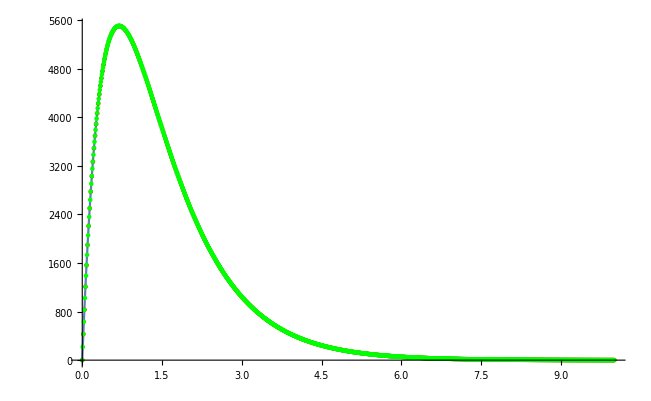

```mathematica
(* Pierwszy przypadek *)
plt1=Plot[y[x] /. rozw1,{x,0,10}];
plt2 = ListPlot[wyn5001, PlotStyle->{Red, PointSize[0.005]}, PlotRange -> All];
plt3 = ListPlot[wyn10001, PlotStyle->{Green, PointSize[0.005]}, PlotRange -> All];
Show[plt1,plt2,plt3]
```

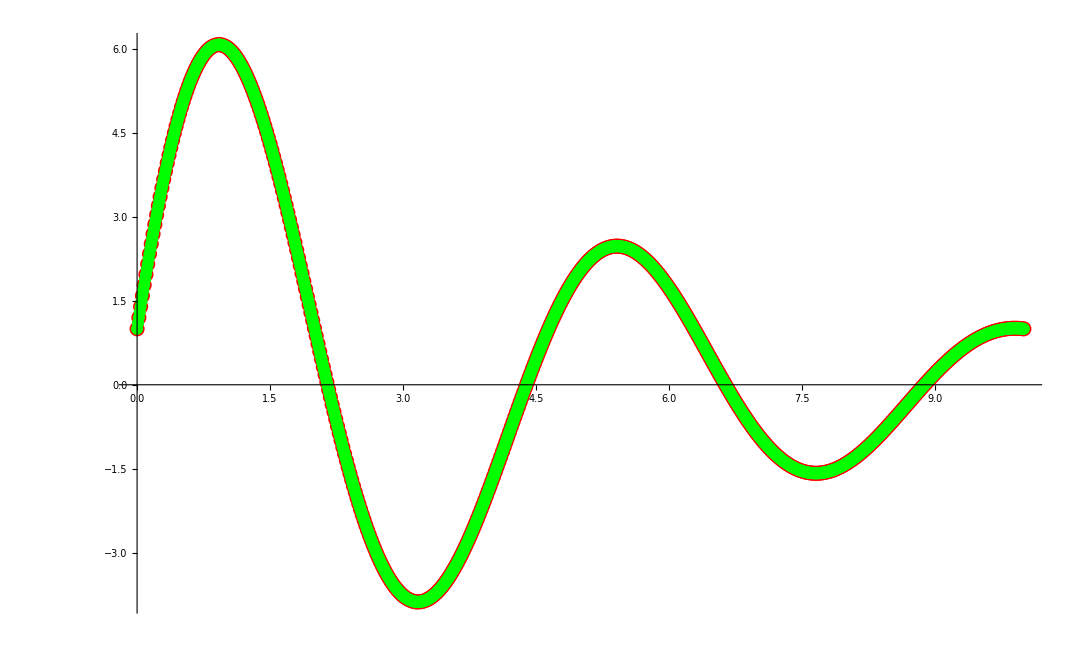

```mathematica
(* Drugi przypadek - zestaw drugi *)
Clear[plt1,plt2,plt3]
m2=5;
k2=2;
s2=10;

ad2[x_]=m2;
bd2[x_]=k2;
cd2[x_]=s2;
dd2[x_]=0;

(* n = 500 *)
wyn5002 = mrsWM[ad2,bd2,cd2,dd2,alfa1,alfa2,beta1,beta2,t1,t2,a,b,n500];
(* n = 1000 *)
wyn10002 = mrsWM[ad2,bd2,cd2,dd2,alfa1,alfa2,beta1,beta2,t1,t2,a,b,n1000];

plt1=Plot[y[x] /. rozw2,{x,0,10}];
plt2 = ListPlot[wyn5002, PlotStyle->{Red, PointSize[0.01]}, PlotRange -> All];
plt3 = ListPlot[wyn10002, PlotStyle->{Green, PointSize[0.008]}, PlotRange -> All];
Show[plt1,plt2,plt3]
```

```mathematica
(* Błędy *)
```

```mathematica
(* Pierwszy przypadek *)
ydok5001 = Table[y[x]/.rozw1[[1]],{x,0,Length[wyn5001], 10/Length[wyn5001]}];
ydok10001 = Table[y[x]/.rozw1[[1]],{x,0,Length[wyn10001],10/Length[wyn5001]}];
ydok10001[[2]] // N
wyn10001[[2,2]]

bledy5001 = Table [{wyn5001[[i,1]], Abs[wyn5001[[i,2]] - N[ydok5001[[i]]]]},{i,1,Length[wyn5001]}];
bledy10001 = Table [{wyn10001[[i,1]], Abs[wyn10001[[i,2]] - N[ydok10001[[i]]]]},{i,1,Length[wyn10001]}];
```

427.669

217.953

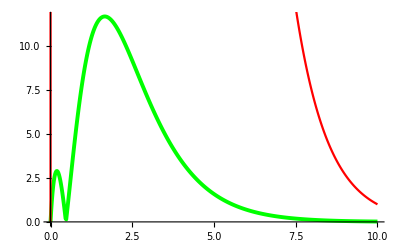

```mathematica
wb5001 = ListPlot[bledy5001, Joined->True, PlotStyle->{Green, Thickness -> 0.007},PlotRange->All];
wb10001 = ListPlot[bledy10001, Joined->True, PlotStyle->{Red, Thickness -> 0.004}, PlotRange->All];
Show[wb5001,wb10001]
```

```mathematica
(* Drugi przypadek *)
ydok5002 = Table[(y[x]/.rozw2[[1]]),{x,1,Length[wyn5002],10/Length[wyn5001]}];
ydok10002 = Table[(y[x]/.rozw2[[1]]),{x,1,Length[wyn10002],10/Length[wyn5001]}];

bledy5002 = Table [{wyn5002[[i,1]], Abs[wyn5002[[i,2]] - ydok5002[[i]]]},{i,1,Length[wyn5002]}];
bledy10002 = Table [{wyn10002[[i,1]], Abs[wyn10002[[i,2]] - ydok10002[[i]]]},{i,1,Length[wyn10002]}];
```

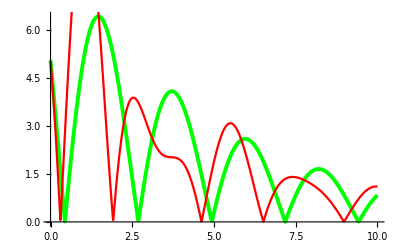

```mathematica
wb5002 = ListPlot[bledy5002, Joined->True, PlotStyle->{Green, Thickness -> 0.007}, PlotRange->All];
wb10002 = ListPlot[bledy10002, Joined->True, PlotStyle->{Red, Thickness -> 0.004}, PlotRange->All];
Show[wb5002,wb10002]
```

```mathematica
(* Błędy maksymalne i średnie dla obu przypadków *)

(* n = 500 *)
max1 = Max[Transpose[bledy5001][[2]]]
mean1 = Mean[Transpose[bledy5001][[2]]]
(* n = 1000 *)
max2 = Max[Transpose[bledy5002][[2]]]
mean2 = Mean[Transpose[bledy5002][[2]]]
(* GraphicsGrid[{{Histogram[{max1,mean1}]},{Histogram[{max2,mean2}]}}] *)
```

11.6895

3.25367

6.42699

2.2394